## Useful functions

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12,Magnification->1.6};
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/31_resonances/code

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=(-1.)^l z SphericalBesselY[l,z];
```

```mathematica
FunctionExpand[RiccatiBesselJ[z,0]]
FunctionExpand[RiccatiBesselN[z,0]]
FunctionExpand[RiccatiBesselJ[z,1]]
FunctionExpand[RiccatiBesselN[z,1]]
```

Sin[z]

-1. Cos[z]

z (-Cos[z]/z+Sin[z]/z^2)

-1. z (-Cos[z]/z^2-Sin[z]/z)

```mathematica
(*Boundery conditions for the wavefunction*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

LEC=(Λ,a_(3-1)^(S-wave) [fm],C_(2-body) [MeV],C_(3-body) [MeV])
the triton-proton S-wave scattering length is used to calibrate the core parameter and
was obtained by R. Lazauskas.

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
a0a1NUCLmartinrimas=Import[NotebookDirectory[]<>"../data/a0-a1_nucl_Rimas-Martin.dat","Table"][[2;;]];
(* λ C0,D0 (Martin, 23) C0,D0 (Rimas, unprojected, 45) C0,Do (Rimas, projected, 67)*)
LECsNUCLmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_nucl_Rimas-Martin.dat","Table"][[2;;]];
LECsUNITmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_univ_Rimas-Martin.dat","Table"][[2;;]];

RefCoreN=Get[LocalObject["Reference_5Gauss_triton_Core_nuclear"]];
RefCoreU=Get[LocalObject["Reference_5Gauss_triton_Core_unitary"]];

activeLEC=LECsUNITmartinrimas[[All,{1,2,3}]](*LECsUNITmartinrimas[[All,{1,2,3}]],LECsNUCLmartinrimas[[All,{1,2,3}]]*);
```

(non)local resonating-group potentials from a 2- and 3-body contact interaction for TRIMER-FERMION (ABC-A)

W_(non-local) takes the Energy (e_) in [MeV]

```mathematica
Integrate[Subscript[c, 1] Subscript[c, 2] Exp[-(Subscript[α, 1]+Subscript[α, 2]) r^2],{r,-Infinity,Infinity},Assumptions->{Subscript[α, 1]∈Reals,Subscript[α, 1]>0,Subscript[α, 2]∈Reals,Subscript[α, 2]>0}]
```

(√π c_1 c_2)/(√(α_1+α_2))

```mathematica
NormTF[core_?ArrayQ]:=1./Sqrt[Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] (Pi/(core[[i]][[2]]+core[[j]][[2]]))^1.5,{i,Length[core]},{j,Length[core]}]]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_]:=Block[{eta2,eta3,w2,w3},
eta2=2. Cc/(2. (Aa+Bb)(3. Aa+3. Bb+2. lam))^(3./2.);
w2=3. (Aa+Bb) lam/(3. (Aa+Bb)+2. lam);
eta3=Dd/(6. (Aa+Bb)^2+16. (Aa+Bb) lam+2. lam^2)^(3./2.);
w3=(3. (Aa+Bb) lam ((Aa+Bb)+2. lam)/(3. (Aa+Bb)^2+8. (Aa+Bb) lam+lam^2));
eta2 Exp[-w2 r^2]+eta3  Exp[-w3 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=(27./64.)(2 (Aa+Bb))^(-3./2.) (1./TwoMyOverHBsq);
a1=(Aa+9. Bb) 3./32.;
b1=(Aa+Bb) 9./16.;
c1=(9. Aa+Bb) 3./32.;

zeta2=-27./32. Cc/(2. (Aa+Bb)+lam)^(3./2.);
zeta3=-27./64. Dd/(2  (Aa+Bb)+5 lam)^(3./2.);

a2=3. (Aa^2+9. Bb^2+10. Aa Bb+(14. Aa+18. Bb) lam)/(16. (2. (Aa+Bb)+lam));	
b2=18. (Aa+Bb) ((Aa+Bb)+2. lam)/(16. (2. (Aa+Bb)+lam));
c2=3. (9. Aa^2+Bb^2+10. Aa Bb+(6. Aa+2. Bb) lam)/(16. (2. (Aa+Bb)+lam));

a3=3. (Aa^2+9. Bb^2+10. Aa Bb+(16. Aa+36. Bb) lam+27. lam^2)/(16. (2. (Aa+Bb)+5. lam));
b3=18. ((Aa+Bb)^2+4. (Aa+Bb) lam+3. lam^2)/(16. (2. (Aa+Bb)+5. lam));
c3=3. (9. Aa^2+Bb^2+10. Aa Bb+(24. Aa+4. Bb) lam+3. lam^2)/(16. (2 (Aa+Bb)+5. lam));

-(4 Pi r rp) (
zeta1 Exp[-a1 r^2-c1 rp^2] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

The function <SolveSecular> expects the variable <<momentum>> in  [fm^-1]
As  W_(non-local) takes the Energy (e_) in [MeV];
The core wave function is parametrized via the "a0={{c_1,α_1},{c_2,α_2},...,{c_N,α_N}}" array:
ϕ_core=(∑^N)_(i=1)c_i·e_^(-α_i/2∏_j (r^-)_j^2)

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=NormTF[a00]^2;

Wmat=ConstantArray[0,{Npoints,Npoints}];

prefac=(*(4 π)^1.5*)1.;
Do[
(*If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,*)

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];

wmat=Table[-prefac hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 
(*Print[(Chop[cij (amat+wmat)])[[1;;4,1;;4]]//MatrixForm];*)
Wmat=Wmat+cij (amat+wmat);

(*]*)
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

numerical and physical parameters

```mathematica
nf={6,4}; (* number form for printing, only *)
k0FM=0.01;  (*initial momentum*)

hbar=197.327053;
Mm=938.92;
m1=3 Mm;m2=Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
sy={"nuclear","unitary"}[[2]];
Print["E_0 = ",(k0FM hbar)^2/(2 μ)," MeV     ℏ^2/(2 SubscriptBox[μ, A = 4]) = ",hbar^2/(2 (Mm^2/(2 Mm)))," MeV·fm^2     ℏ^2/(2 SubscriptBox[μ, A = 2]) = ",1/mh2]
λRange=Range[1,Length[activeLEC]];
```

E_0 = 0.00276473 MeV     ℏ^2/(2 SubscriptBox[μ, A = 4]) = 41.471 MeV·fm^2     ℏ^2/(2 SubscriptBox[μ, A = 2]) = 27.6473

```mathematica
findLogDivisions[{xmin_,xmax_},n_Integer]:=10^FindDivisions[Log10@{xmin,xmax},n]

GetERE[x_,l_]:=Module[{localcore=x,locall=l},

core=localcore;

dataS={};dataP={};
tanDsL={};tanDpL={};
tanDs={};tanDp={};

SetSharedVariable[tanDs,tanDp];

ParallelDo[
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecular[rr,nGrid,momFM,0,locall,C0,D0,core,mh2];
TanDelPwave=SolveSecular[rr,nGrid,momFM,1,locall,C0,D0,core,mh2];
AppendTo[tanDs,{energ,TanDelSwave}];
AppendTo[tanDp,{energ,TanDelPwave}];
,{energ,ErangeMeV}];

tanDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
tanDp=Reverse[Sort[tanDp,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
(*AppendTo[tanDsL,tnDs];
AppendTo[tanDpL,tnDp];*)
(*Extract the ERE Parameters*)
Lrel = 0;
dataS=Transpose[{Sqrt[mh2 ErangeMeV],Sqrt[mh2 ErangeMeV]/Re[tanDs⟦All,2⟧]}];
EreS=Fit[dataS⟦f1;;f2⟧,{1,p^2},p];
a0tf=-Coefficient[EreS,p,0]^-1;
r0tf= Coefficient[EreS,p,2]*2.;
ShaS=Fit[dataS⟦f1;;f2⟧,{1,p^2,p^4},p];
a0tfs=-Coefficient[ShaS,p,0]^-1;
r0tfs= Coefficient[ShaS,p,2]*2.;
p0tfs= Coefficient[ShaS,p,4];
Lrel = 1;
dataP=Transpose[{Sqrt[mh2 ErangeMeV],Sqrt[mh2 ErangeMeV]^3/Re[tanDp⟦All,2⟧]}];
EreP=Fit[dataP⟦f1;;f2⟧,{1,p^2},p];
a1tf=-Coefficient[EreP,p,0]^-1;
r1tf= Coefficient[EreP,p,2]*2.;
ShaP=Fit[dataP⟦f1;;f2⟧,{1,p^2,p^4},p];
a1tfs=-Coefficient[ShaP,p,0]^-1;
r1tfs= Coefficient[ShaP,p,2]*2.;
p1tfs= Coefficient[ShaP,p,4];
(*Print["dataS = ", dataS];*)
{a0tf,r0tf,a1tf,r1tf,a0tfs,r0tfs,p0tfs,a1tfs,r1tfs,p1tfs,dataS,dataP}
]
```

```mathematica
PlotERE:=Module[{},(*Plot the Phaseshifts for each α and C that I used*)
phaseS=Transpose[{tanDs⟦All,1⟧, ArcTan[tanDs⟦All,2⟧]}];
phaseP=Transpose[{tanDp⟦All,1⟧, ArcTan[tanDp⟦All,2⟧]}];
(*---------*)
Tfits=(Fit[dataS⟦1;;Min[10,Length[dataS]]⟧,{1,p^2,p^4},p]); (*fit ere again*)
dataTS=dataS;dataTS⟦All,2⟧=dataTS⟦All,2⟧^-1 ;
Polesp=(p/.NSolve[Tfits-ⅈ p==0,{p}]) ; (*find pole positions*) PolesE=hbar^2 Polesp^2 / (2 μ);
Print["S Pole Poitions in momentum: ", Polesp];
Print["S Pole Poitions in energy:   ", PolesE];
(*---------*)
Tfitp=(Fit[dataP⟦1;;Min[10,Length[dataP]]⟧,{1,p^2,p^4},p]); (*fit ere again*)
dataTP=dataP;dataTP⟦All,2⟧=dataTP⟦All,2⟧^-1 ;
Polepp=(p/.NSolve[Tfitp-ⅈ p^3==0,{p}]) ; (*find pole positions*) PolepE=hbar^2 Polepp^2 / (2 μ);
Print["P Pole Poitions in momentum: ", Polepp];
Print["P Pole Poitions in energy:   ", PolepE];
Print[Tfits];
Print[Tfitp];
GraphicsGrid[{{
Show[{ Plot[-(1/a0tf)+(1/2)r0tf k^2,{k,0,dataS⟦-1,1⟧}],ListPlot[dataS,PlotRange->{{dataS⟦1,1⟧,dataS⟦1,-1⟧},All}]},ImageSize->500,AxesLabel->{"E [MeV]","K CotTan[δ_(S - wave)] [fm^-1]"},PlotStyle->"Red", PlotLabel->" S-wave KCotδ compared with -1/a0+1/2r0 k^2"]
,
Show[{ Plot[-(1/a1tf)+(1/2)r1tf k^2,{k,0,dataP⟦-1,1⟧}],ListPlot[dataP,PlotRange->{{dataP⟦1,1⟧,dataP⟦1,-1⟧},All}]},ImageSize->500,AxesLabel->{"E [MeV]","K^3 CotTan[δ_(S - wave)] [fm^-3]"},PlotStyle->"Red",PlotLabel->" P-wave K^3Cotδ compared with -1/a0+1/2r0 k^2"]

},
{
Show[ListPlot[dataTS],Plot[Tfits^-1,{p,0,0.4},PlotRange->{Automatic,Automatic}],ImageSize->500,PlotLabel->"T matrix compared with the ERE^-1(O(k^4)) expansion"],
Show[ListPlot[dataTP],Plot[Tfitp^-1,{p,0,0.4},PlotRange->{Automatic,Automatic}],ImageSize->500,PlotLabel->"T matrix compared with the ERE^-1(O(k^4)) expansion"]

}
},ImageSize->1000]//Print
]
```

## Import density and fit wavefunctions

```mathematica
tailweight=0;
wflambdasN={1.0,2.0,3.0,4.0,6.0,8.0,10.0};
Martinϕnucl=Cases[Import["../data/abc_u_"<>ToString[NumberForm[#,{12,1}]]<>"_binf_r1b.dnst","Table"],{_?NumberQ,___}]&/@wflambdasN;
MϕN=Transpose[{#⟦All,1⟧,Sqrt[#⟦All,3⟧]}]&/@Martinϕnucl;
wflambdasU={1.5,2.0,3.0,4.0,6.0,8.0,10.0};
Martinϕunit=Cases[Import["../data/abc_univ_"<>ToString[NumberForm[#,{12,1}]]<>"_binf_r1b.dnst","Table"],{_?NumberQ,___}]&/@wflambdasU;
MϕU=Transpose[{#⟦All,1⟧,Sqrt[#⟦All,3⟧]}]&/@Martinϕunit;
If[sy=="unitary",
Mϕ=MϕU;
wflambdas=wflambdasU;
,
Mϕ=MϕN;
wflambdas=wflambdasN;]
```

λ=1.5  , core={{0.120087,0.415664},{0.0191999,0.110958},{0.165483,1.40952}}

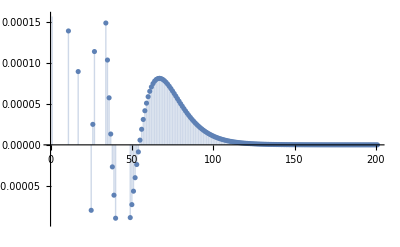

λ=2.  , core={{0.202178,1.86122},{0.136821,0.498224},{0.0226785,0.123335}}

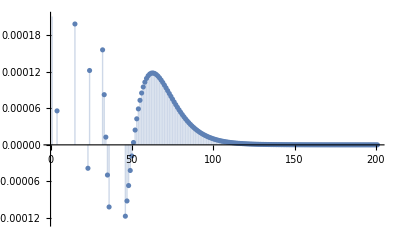

λ=3.  , core={{0.0185386,0.117347},{0.292409,2.14993},{0.126239,0.479901}}

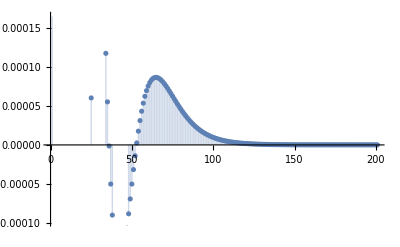

λ=4.  , core={{0.0122654,0.100415},{0.361736,2.14998},{0.106754,0.405478}}

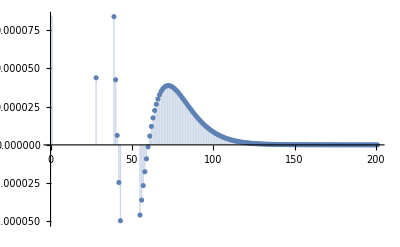

λ=6.  , core={{0.109434,2.14997},{0.3377,2.14999},{0.0855893,0.267003}}

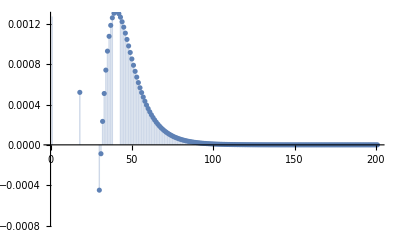

λ=8.  , core={{0.121078,2.14999},{0.361013,2.15},{0.0773416,0.253037}}

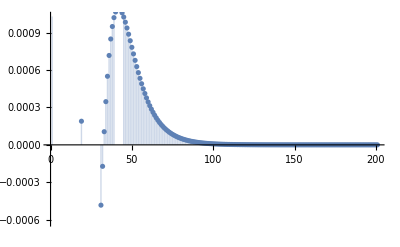

λ=10.  , core={{0.507174,2.15},{0.0000173493,2.07224},{0.0718572,0.244247}}

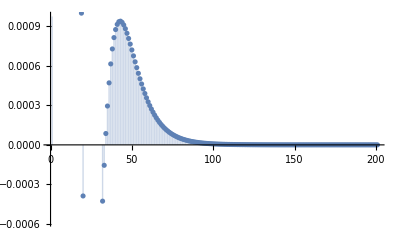

```mathematica
nk=3;

rmip=0.0;
rmap=21;

wfCores={};
wfs={};
w1=1;
amax=10^1;amin=0;
bmin=0.0;bmax=2.15;
w2=Min[Length[#]&/@Mϕ];
Do[
data=Mϕ[[ll]][[w1;;w2]];

modelGauss={Sum[aLn@i Exp[-bLn@i rrel^2],{i,nk}],Table[{amin<aLn@i <amax,bmin<bLn@i <bmax},{i,nk}]};
nlmLABC=NonlinearModelFit[data,modelGauss,Flatten[Table[{{aLn@i,RandomReal[{-0.1,0.1}]},{bLn@i,RandomReal[{0.0001,0.5}]}},{i,nk}],1],rrel,Weights->((#+1)^3&/@data[[All,1]])];
nlresi=nlmLABC["FitResiduals"];
(*modelGauss=Sum[aLn@i Exp[-bLn@i rrel^2],{i,nk}];
nlmLABC=NonlinearModelFit[data,modelGauss,Flatten[Table[{{aLn@i,RandomReal[{-10.1,10.1}]},{bLn@i,RandomReal[{0.0001,0.25}]}},{i,nk}],1],rrel];*)
basispara=Table[{aLn@i,bLn@i},{i,nk}]/.nlmLABC["BestFitParameters"];
AppendTo[wfCores,basispara];
AppendTo[wfs,Normal[nlmLABC]];

Print["λ=",wflambdas[[ll]],"  , core=",wfCores[[-1]]];
GraphicsGrid[{{
Show[ListLogLogPlot[Mϕ[[ll]],PlotLabel->"Λ = "<>ToString[wflambdas[[ll]]]<>" fm^-1"<>"  ;  f_fit=∑_(n = 1)^N c_n·e^(-SubscriptBox[α, n]·SuperscriptBox[ρ, 2]) with N="<>ToString[nk]<>"    Case: "<>ToString[sy]],
LogLogPlot[wfs[[-1]],{rrel,rmip,rmap},PlotLegends->{"original Ψ"},PlotRange->Full, AxesLabel->{"r [fm]","WaveFunction"}],ImageSize->Scaled[.8]],ListPlot[nlresi,Filling->Axis],
Plot[wfs[[-1]],{rrel,rmip,rmap},PlotLegends->{"original Ψ"},PlotRange->Full,Epilog->Map[Point,Mϕ[[ll]]], AxesLabel->{"r [fm]","WaveFunction"},ImageSize->Scaled[.8]]
}},ImageSize->{{1200},{1700}}]//Print
,{ll,Range[Length[wflambdas]]}];
```

## The real pudding

```mathematica
rGrid= {21.3}(*Subdivide[6.5,22.1,2]*); 
rr=rGrid[[1]];
EREs={};
lRange=Range[1,Length[wflambdas]];

nGrid=100;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.002;
k0FMax=1.5;
Divisions=20;
rmip=0.0;
rmap=16;
(*---------------------*)
ErangeMeV=N[findLogDivisions[{k0FMin^2/mh2,k0FMax^2/mh2},Divisions]];
Erange1onfm=Sqrt[mh2 ErangeMeV];
exportdata={};
```

nn=4  nwf=1  λ=0.5625  C0=-86.4495  D0=79.22  core={{0.165483,1.40952},{0.120087,0.415664},{0.0191999,0.110958}}

S Pole Poitions in momentum: {-1.29294-0.425237 ⅈ,-0.165202+0.425237 ⅈ,0.165202+0.425237 ⅈ,1.29294-0.425237 ⅈ}

S Pole Poitions in energy:   {41.2184+30.4013 ⅈ,-4.24482-3.88446 ⅈ,-4.24482+3.88446 ⅈ,41.2184-30.4013 ⅈ}

P Pole Poitions in momentum: {-0.158822-0.501105 ⅈ,0.+0.368895 ⅈ,0.+1.09164 ⅈ,0.158822-0.501105 ⅈ}

P Pole Poitions in energy:   {-6.24503+4.40071 ⅈ,-3.76234+0. ⅈ,-32.9469+0. ⅈ,-6.24503-4.40071 ⅈ}

-0.275679+0.956247 p^2-0.715043 p^4

0.242793+1.71216 p^2+2.18184 p^4

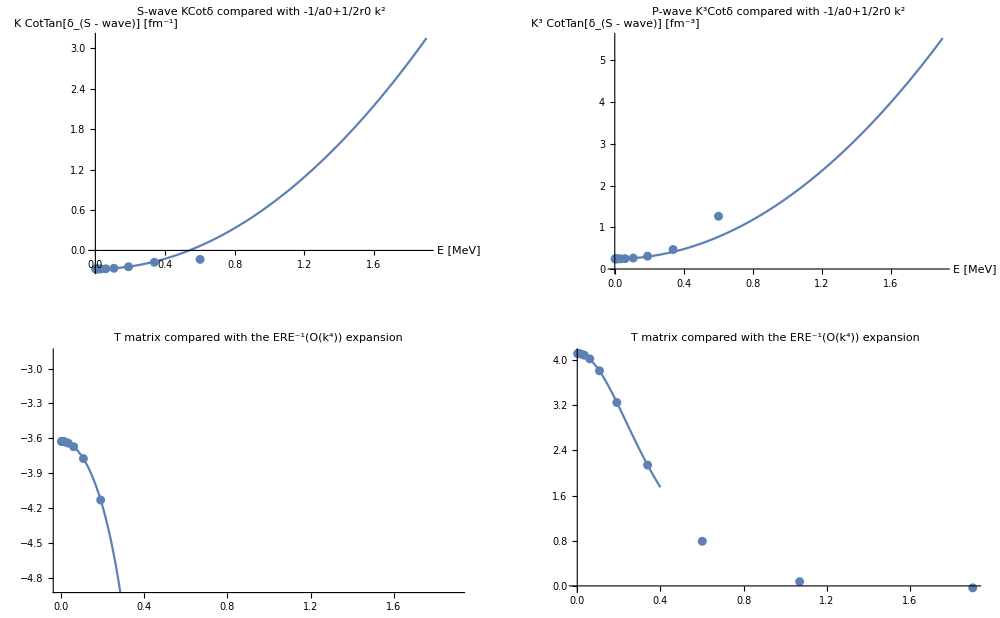

λ = Λ^2/4 = 0.5625 ; R_max = 21.3000:   a0 = 3.62755     r0 = 1.89736     a1 = -4.11617     r1 = 2.92788

λ = Λ^2/4 = 0.5625 ; R_max = 21.3000:   a0 = 3.62755     r0 = 1.89758     a1 = -4.11617     r1 = 2.91972     p0 = -0.869898     p1 = 33.2033

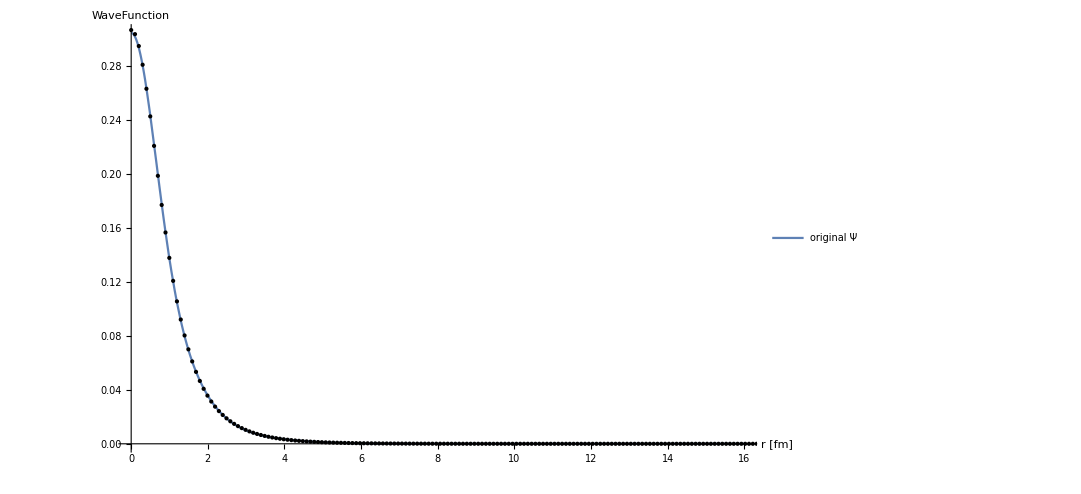

nn=5  nwf=2  λ=1.  C0=-142.363  D0=173.925  core={{0.202178,1.86122},{0.0226785,0.123335},{0.136821,0.498224}}

S Pole Poitions in momentum: {-1.16386-0.441065 ⅈ,-0.171817+0.441065 ⅈ,0.171817+0.441065 ⅈ,1.16386-0.441065 ⅈ}

S Pole Poitions in energy:   {32.0715+28.3848 ⅈ,-4.5623-4.19037 ⅈ,-4.5623+4.19037 ⅈ,32.0715-28.3848 ⅈ}

P Pole Poitions in momentum: {-0.147692-0.530586 ⅈ,0.+0.394621 ⅈ,0.+1.03705 ⅈ,0.147692-0.530586 ⅈ}

P Pole Poitions in energy:   {-7.18026+4.33306 ⅈ,-4.30539+0. ⅈ,-29.7338+0. ⅈ,-7.18026-4.33306 ⅈ}

-0.296949+0.851262 p^2-0.855536 p^4

0.335056+2.17728 p^2+2.69909 p^4

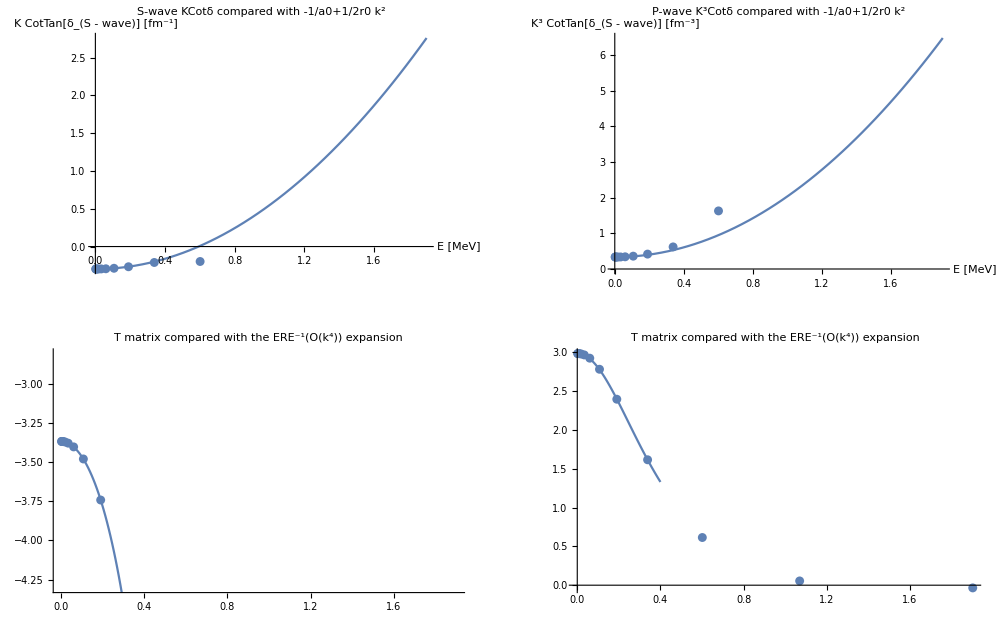

λ = Λ^2/4 = 1.0000 ; R_max = 21.3000:   a0 = 3.36771     r0 = 1.68921     a1 = -2.98195     r1 = 3.39659

λ = Λ^2/4 = 1.0000 ; R_max = 21.3000:   a0 = 3.36771     r0 = 1.68949     a1 = -2.98195     r1 = 3.38118     p0 = -1.14083     p1 = 62.7342

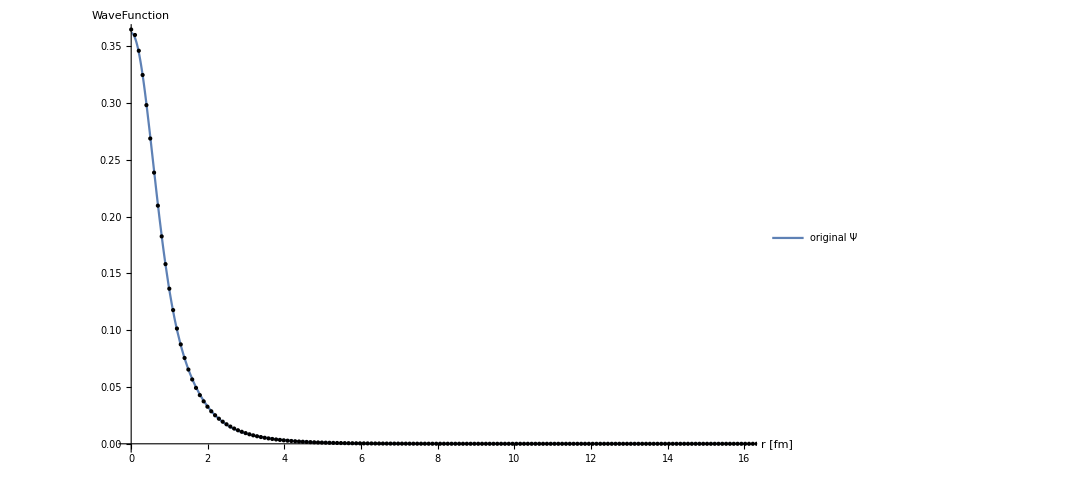

nn=6  nwf=3  λ=2.25  C0=-295.93  D0=566.65  core={{0.0185386,0.117347},{0.292409,2.14993},{0.126239,0.479901}}

S Pole Poitions in momentum: {-1.02869-0.440493 ⅈ,-0.168819+0.440493 ⅈ,0.168819+0.440493 ⅈ,1.02869-0.440493 ⅈ}

S Pole Poitions in energy:   {23.8921+25.0558 ⅈ,-4.57659-4.11192 ⅈ,-4.57659+4.11192 ⅈ,23.8921-25.0558 ⅈ}

P Pole Poitions in momentum: {-0.142357-0.508651 ⅈ,0.+0.407982 ⅈ,0.+0.836636 ⅈ,0.142357-0.508651 ⅈ}

P Pole Poitions in energy:   {-6.5928+4.0039 ⅈ,-4.60187+0. ⅈ,-19.352+0. ⅈ,-6.5928-4.0039 ⅈ}

-0.307186+0.77014 p^2-1.10234 p^4

0.41893+2.84112 p^2+4.39919 p^4

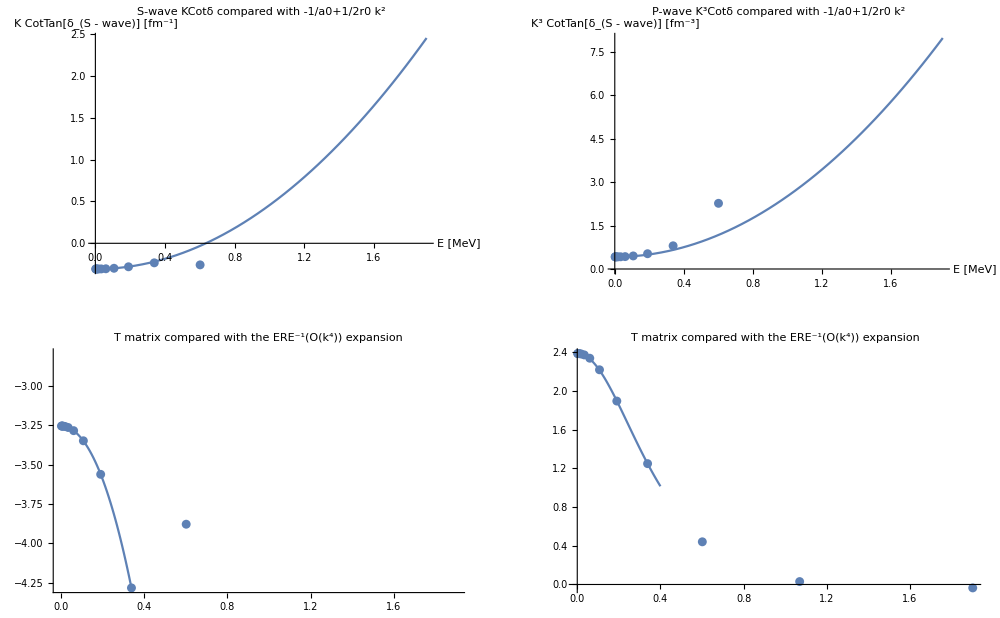

λ = Λ^2/4 = 2.2500 ; R_max = 21.3000:   a0 = 3.25547     r0 = 1.52669     a1 = -2.3844     r1 = 4.18138

λ = Λ^2/4 = 2.2500 ; R_max = 21.3000:   a0 = 3.25547     r0 = 1.52705     a1 = -2.3844     r1 = 4.15726     p0 = -1.43034     p1 = 98.1491

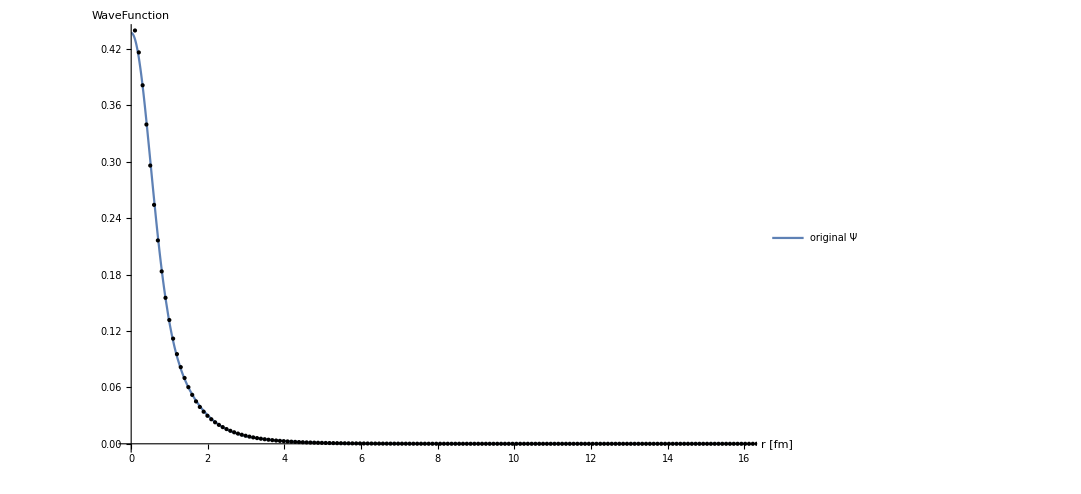

nn=7  nwf=4  λ=4.  C0=-505.15  D0=1426.75  core={{0.0122654,0.100415},{0.106754,0.405478},{0.361736,2.14998}}

S Pole Poitions in momentum: {-0.925571-0.425444 ⅈ,-0.159173+0.425444 ⅈ,0.159173+0.425444 ⅈ,0.925571-0.425444 ⅈ}

S Pole Poitions in energy:   {18.6807+21.7739 ⅈ,-4.30376-3.74452 ⅈ,-4.30376+3.74452 ⅈ,18.6807-21.7739 ⅈ}

P Pole Poitions in momentum: {-0.147385-0.457538 ⅈ,0.+0.414754 ⅈ,0.+0.645486 ⅈ,0.147385-0.457538 ⅈ}

P Pole Poitions in energy:   {-5.18715+3.72874 ⅈ,-4.75592+0. ⅈ,-11.5193+0. ⅈ,-5.18715-3.72874 ⅈ}

-0.302686+0.735123 p^2-1.41366 p^4

0.426133+3.24746 p^2+6.8887 p^4

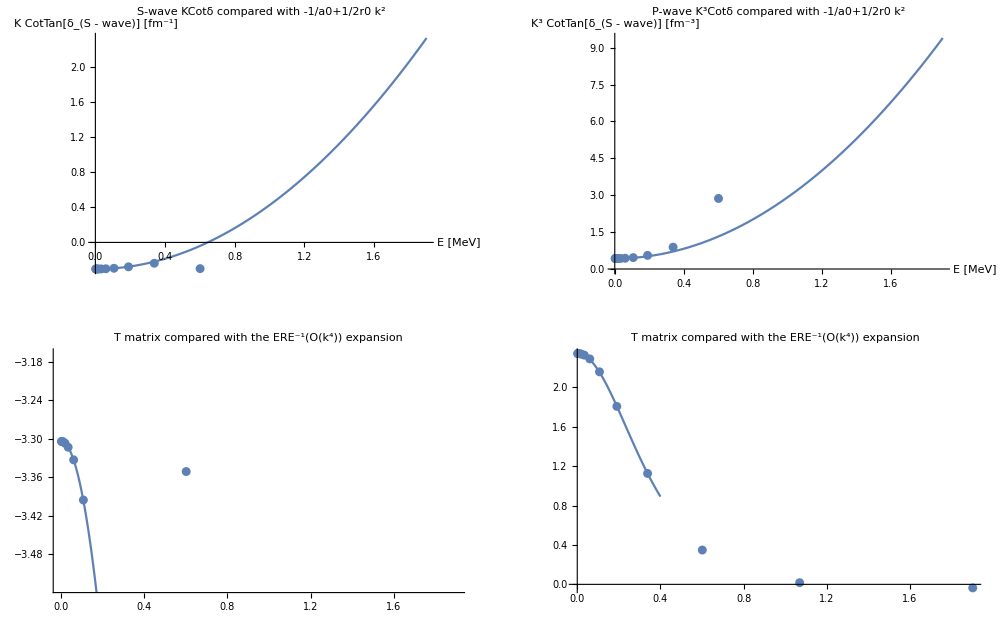

λ = Λ^2/4 = 4.0000 ; R_max = 21.3000:   a0 = 3.30389     r0 = 1.45432     a1 = -2.34408     r1 = 4.95619

λ = Λ^2/4 = 4.0000 ; R_max = 21.3000:   a0 = 3.30389     r0 = 1.45473     a1 = -2.34408     r1 = 4.93105     p0 = -1.67126     p1 = 102.296

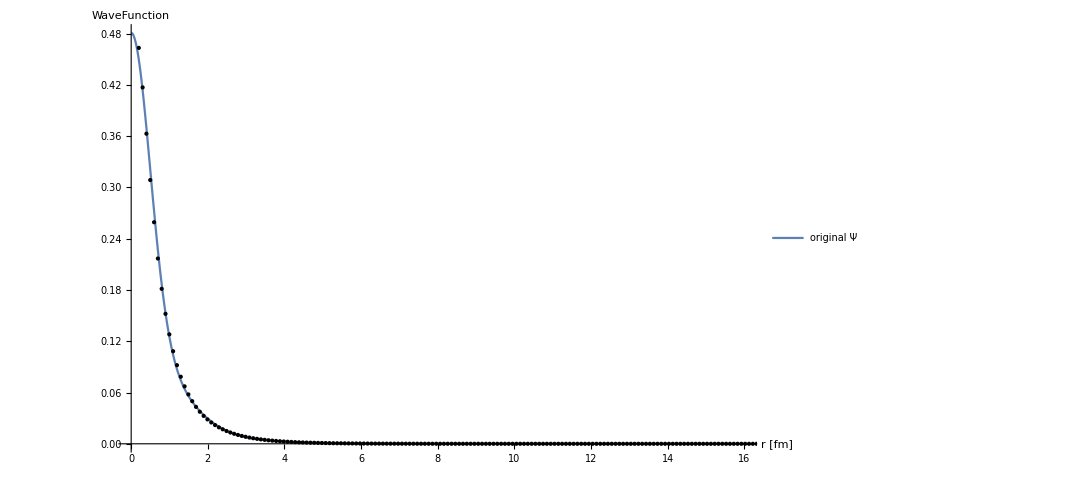

nn=8  nwf=5  λ=9.  C0=-1090.55  D0=6552.5  core={{0.00671914,0.0800485},{0.43452,2.14999},{0.0880636,0.332441}}

S Pole Poitions in momentum: {-0.811855-0.406764 ⅈ,-0.144779+0.406764 ⅈ,0.144779+0.406764 ⅈ,0.811855-0.406764 ⅈ}

S Pole Poitions in energy:   {13.6482+18.2602 ⅈ,-3.99494-3.25635 ⅈ,-3.99494+3.25635 ⅈ,13.6482-18.2602 ⅈ}

P Pole Poitions in momentum: {-0.147641-0.395051 ⅈ,-0.0770053+0.436648 ⅈ,0.0770053+0.436648 ⅈ,0.147641-0.395051 ⅈ}

P Pole Poitions in energy:   {-3.71214+3.22509 ⅈ,-5.10733-1.85924 ⅈ,-5.10733+1.85924 ⅈ,-3.71214-3.22509 ⅈ}

-0.296087+0.67255 p^2-1.92622 p^4

0.4203+3.79282 p^2+12.0202 p^4

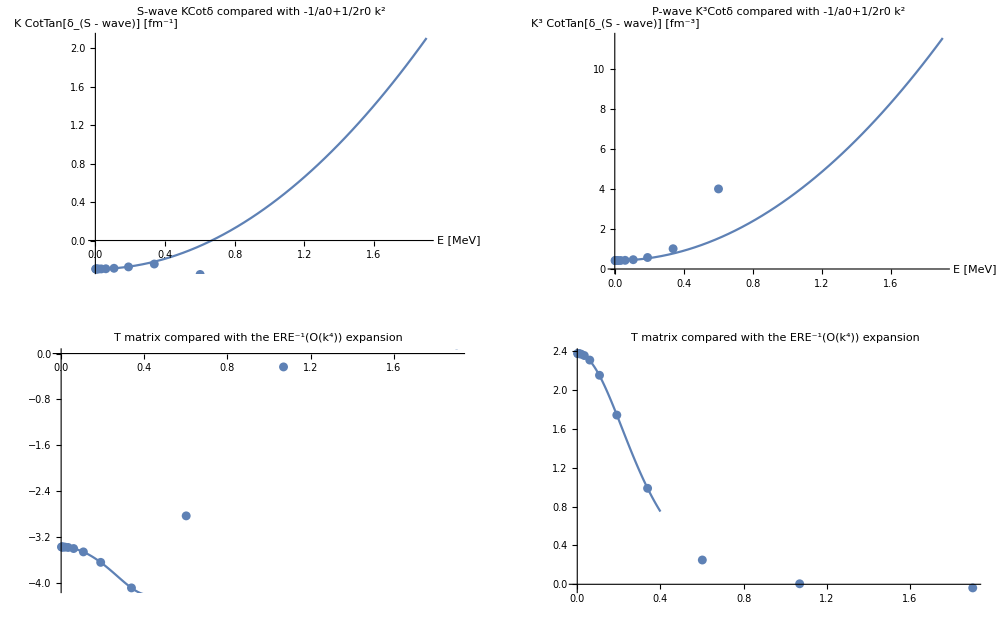

λ = Λ^2/4 = 9.0000 ; R_max = 21.3000:   a0 = 3.37753     r0 = 1.32778     a1 = -2.37677     r1 = 6.14159

λ = Λ^2/4 = 9.0000 ; R_max = 21.3000:   a0 = 3.37753     r0 = 1.3283     a1 = -2.37677     r1 = 6.11663     p0 = -2.11405     p1 = 101.553

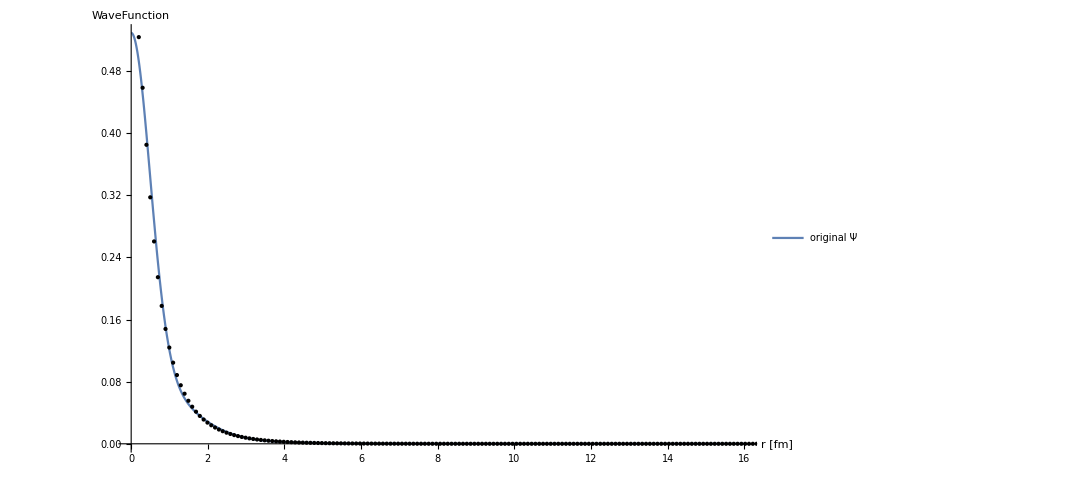

nn=9  nwf=6  λ=16.  C0=-1898.55  D0=25697.  core={{0.00447568,0.0690372},{0.0789223,0.298769},{0.473648,2.14999}}

S Pole Poitions in momentum: {-0.750309-0.398567 ⅈ,-0.134138+0.398567 ⅈ,0.134138+0.398567 ⅈ,0.750309-0.398567 ⅈ}

S Pole Poitions in energy:   {11.1725+16.5358 ⅈ,-3.89448-2.95622 ⅈ,-3.89448+2.95622 ⅈ,11.1725-16.5358 ⅈ}

P Pole Poitions in momentum: {-0.145333-0.360099 ⅈ,-0.106506+0.389642 ⅈ,0.106506+0.389642 ⅈ,0.145333-0.360099 ⅈ}

P Pole Poitions in energy:   {-3.00111+2.89381 ⅈ,-3.88382-2.29469 ⅈ,-3.88382+2.29469 ⅈ,-3.00111-2.89381 ⅈ}

-0.29385+0.605976 p^2-2.30195 p^4

0.416416+4.18516 p^2+16.9247 p^4

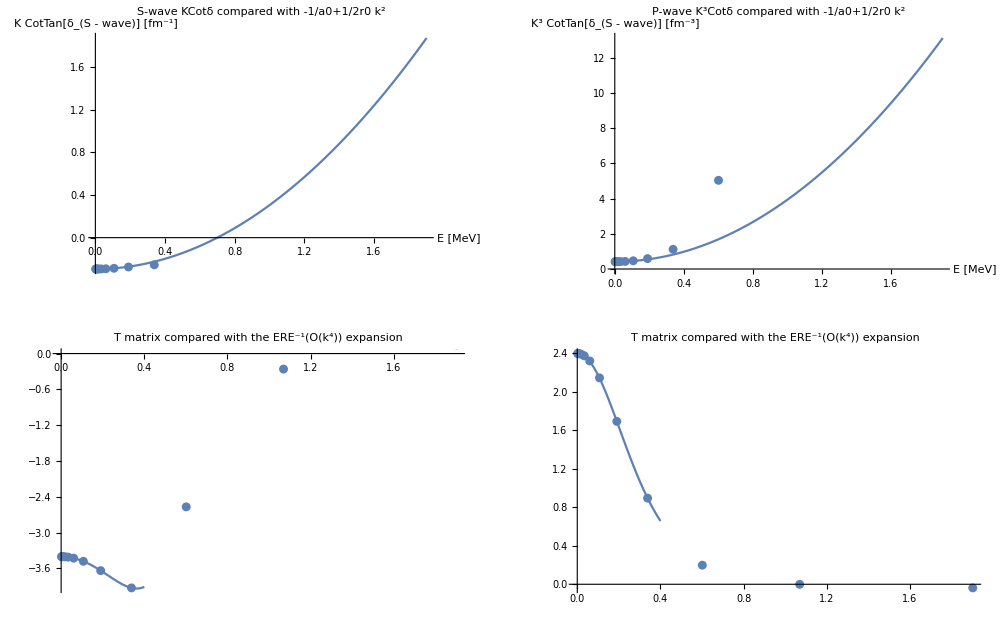

λ = Λ^2/4 = 16.0000 ; R_max = 21.3000:   a0 = 3.40322     r0 = 1.19733     a1 = -2.39916     r1 = 7.02097

λ = Λ^2/4 = 16.0000 ; R_max = 21.3000:   a0 = 3.40322     r0 = 1.19795     a1 = -2.39916     r1 = 6.99595     p0 = -2.51594     p1 = 101.793

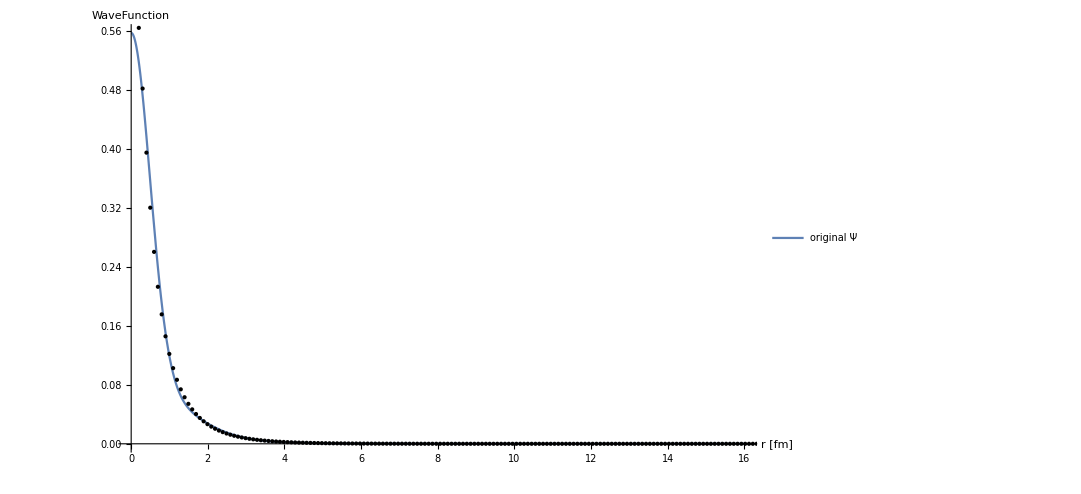

nn=10  nwf=7  λ=25.  C0=-2929.17  D0=92495.  core={{0.0032234,0.0617361},{0.50104,2.15},{0.0730043,0.278746}}

S Pole Poitions in momentum: {-0.708358-0.396802 ⅈ,-0.124074+0.396802 ⅈ,0.124074+0.396802 ⅈ,0.708358-0.396802 ⅈ}

S Pole Poitions in energy:   {9.51951+15.5421 ⅈ,-3.92752-2.72232 ⅈ,-3.92752+2.72232 ⅈ,9.51951-15.5421 ⅈ}

P Pole Poitions in momentum: {-0.142859-0.336777 ⅈ,-0.11659+0.359573 ⅈ,0.11659+0.359573 ⅈ,0.142859-0.336777 ⅈ}

P Pole Poitions in energy:   {-2.57148+2.66032 ⅈ,-3.19878-2.3181 ⅈ,-3.19878+2.3181 ⅈ,-2.57148-2.66032 ⅈ}

-0.2952+0.524005 p^2-2.59073 p^4

0.419419+4.55499 p^2+21.9337 p^4

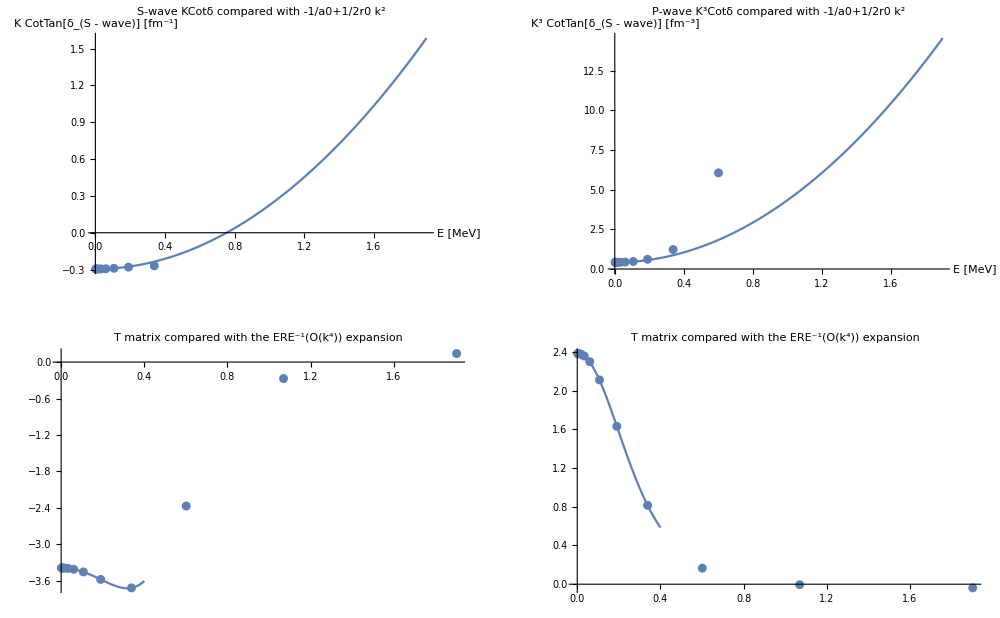

λ = Λ^2/4 = 25.0000 ; R_max = 21.3000:   a0 = 3.38762     r0 = 1.03985     a1 = -2.38217     r1 = 7.81469

λ = Λ^2/4 = 25.0000 ; R_max = 21.3000:   a0 = 3.38762     r0 = 1.04057     a1 = -2.38217     r1 = 7.78883     p0 = -2.91733     p1 = 105.236

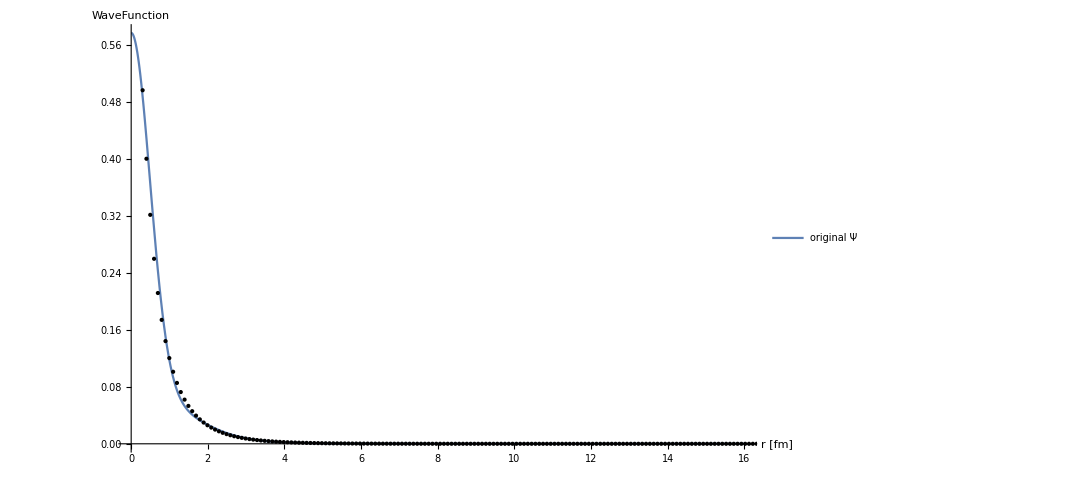

```mathematica
Do[
Do[
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==wflambdas[[ll]]&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
mycore=wfCores[[ll]];
Print["nn=",nn,"  nwf=",ll,"  λ=",λ,"  C0=",C0,"  D0=",D0,"  core=",mycore];
ERE=GetERE[mycore,λ];
PlotERE;
AppendTo[EREs,ERE];
Print["λ = Λ^2/4 = ",NumberForm[λ,nf](*,"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]*)," ; R_max = ",NumberForm[rr,nf],":   a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧];
Print["λ = Λ^2/4 = ",NumberForm[λ,nf](*,"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]*)," ; R_max = ",NumberForm[rr,nf],":   a0 = ", ERE⟦5⟧,"     r0 = ", ERE⟦6⟧,"     a1 = ", ERE⟦8⟧,"     r1 = ", ERE⟦9⟧,"     p0 = ", ERE⟦7⟧,"     p1 = ", ERE⟦10⟧];
tmpwfs=Total[#⟦1⟧ⅇ^(-#⟦2⟧ r^2)&/@mycore];
Plot[tmpwfs,{r,rmip,rmap},PlotLegends->{"original Ψ"},PlotRange->Full,Epilog->Map[Point,Mϕ[[ll]]], AxesLabel->{"r [fm]","WaveFunction"},ImageSize->800]//Print;
AppendTo[exportdata,Join[{λ,nGrid,rr},ERE[[;;10]],Polesp,PolesE,Polepp,PolepE,Flatten[mycore]]];
,{ll,lRange}];
,{rr,rGrid}];
Export["/tmp/tmp.dat",exportdata,"Table"];
```

```mathematica
model=a+b/x+c/x^2;
l0=2;
lambdas=exportdata[[All,1]];
a0s=Transpose[{lambdas,exportdata[[All,4]]}];
fita0=model/.FindFit[a0s[[l0;;]],model,{a,b,c},x];
r0s=Transpose[{wflambdas,exportdata[[All,5]]}];
fitr0=model/.FindFit[r0s[[l0;;]],model,{a,b,c},x];
a1s=Transpose[{wflambdas,exportdata[[All,6]]}];
fita1=model/.FindFit[a1s[[l0;;]],model,{a,b,c},x];
r1s=Transpose[{wflambdas,exportdata[[All,7]]}];
fitr1=model/.FindFit[r1s[[l0;;]],model,{a,b,c},x];
legs="R_max="<>ToString[rr];
GraphicsGrid[{{
Show[ListPlot[a0s,PlotLegends->Placed[legs,Above],AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["a_S [\\textrm{fm}]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) a_S = "<>ToString[Limit[fita0,x->Infinity]]<>" fm"],Plot[fita0,{x,0,lambdas[[-1]]},ImageSize->Large]],
Show[ListPlot[r0s,AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["r_S [\\textrm{fm}]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) r_S = "<>ToString[Limit[fitr0,x->Infinity]]<>" fm"],Plot[fitr0,{x,0,10},ImageSize->Large]]
},{
Show[ListPlot[a1s,PlotLegends->Placed[legs,Above],AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["a_P [\\textrm{fm}^3]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) a_P = "<>ToString[Limit[fita1,x->Infinity]]<>" fm^3"],Plot[fita1,{x,0,lambdas[[-1]]},ImageSize->Large]],
Show[ListPlot[r1s,AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["r_P [\\textrm{fm}^{-1}]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) r_P = "<>ToString[Limit[fitr1,x->Infinity]]<>" fm^-1"],Plot[fitr1,{x,0,lambdas[[-1]]},ImageSize->Large]]
}}]
```

-Graphics-

```mathematica
ComplexPlot
```

```mathematica
cplxpoleSp=Transpose[{Re[exportdata[[All,14+#]]],Im[exportdata[[All,14+#]]]}]&/@{0,1,2,3};
cplxpolePp=Transpose[{Re[exportdata[[All,22+#]]],Im[exportdata[[All,22+#]]]}]&/@{0,1,2,3};
GraphicsGrid[{{
Show[ListPlot[#->exportdata[[All,1]],PlotRange->{{-0.5,0.5},{-0.5,0.5}},AxesLabel->{"Re[k_res] [fm^-1]","Im[k_res] [fm^-1]"}]&/@cplxpoleSp]
,
Show[ListPlot[#->exportdata[[All,1]],PlotRange->{{-0.5,0.5},{-0.5,0.5}},AxesLabel->{"Re[k_res] [fm^-1]","Im[k_res] [fm^-1]"}]&/@cplxpolePp]
}}
]
```

-Graphics-

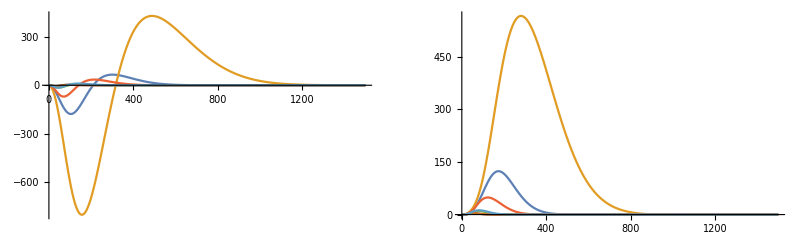

```mathematica
plts={};
pltp={};
Do[
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==wflambdas[[nwf]]&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;
C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
mycore=wfCores[[nwf]];
rMax=15;
eplot=ErangeMeV[[1]];
AppendTo[plts,
Chop[Table[WnolocTF[rr,rr,ErangeMeV[[2]],λ,C0,D0,mycore[[1]][[2]],mycore[[1]][[2]],0,mh2]
,{rr,0.01,rMax,0.01}]]
];
AppendTo[pltp,
Chop[Table[WnolocTF[rr,rr,ErangeMeV[[2]],λ,C0,D0,mycore[[1]][[2]],mycore[[1]][[2]],1,mh2]
,{rr,0.01,rMax,0.01}]]
]
,{nwf,Range[Length[wflambdas]]}]
GraphicsGrid[{{
ListPlot[plts[[1;;7]],Joined->True,PlotRange->Full],
ListPlot[pltp[[1;;7]],Joined->True,PlotRange->Full]
}}]
(*GraphicsGrid[{{
Plot3D[{(*WnolocTF[rr,rp,ErangeMeV[[-1]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2],*)WnolocTF[rr,rp,ErangeMeV[[-1]],λ,C0,D0,mycore[[1]][[2]],mycore[[1]][[2]],1,mh2]},{rr,0.1,rMax},{rp,0.1,rMax},PlotRange->Full,PlotLegends->{"E="<>ToString[eplot],"E="<>ToString[eplot]},PlotStyle->{Directive[Opacity[0.2],Orange, Specularity[White,50]],None},ImageSize->Scaled[.8]],Plot3D[{(*WnolocTF[rr,rp,ErangeMeV[[-1]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2],*)WnolocTF[rr,rp,ErangeMeV[[-1]],λ,C0,D0,mycore[[2]][[2]],mycore[[2]][[2]],1,mh2]},{rr,0.1,rMax},{rp,0.1,rMax},PlotRange->Full,PlotLegends->{"E="<>ToString[eplot],"E="<>ToString[eplot]},PlotStyle->{Directive[Opacity[0.2],Orange, Specularity[White,50]],None},ImageSize->Scaled[.8]]},{
Plot3D[{(*WnolocTF[rr,rp,ErangeMeV[[-1]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2],*)WnolocTF[rr,rp,ErangeMeV[[-1]],λ,C0,D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2]},{rr,0.1,rMax},{rp,0.1,rMax},PlotRange->Full,PlotLegends->{"E="<>ToString[eplot],"E="<>ToString[eplot]},PlotStyle->{Directive[Opacity[0.2],Orange, Specularity[White,50]],None},ImageSize->Scaled[.8]],Plot3D[{(*WnolocTF[rr,rp,ErangeMeV[[-1]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2],*)WnolocTF[rr,rp,ErangeMeV[[-1]],λ,C0,D0,mycore[[2]][[2]],mycore[[1]][[2]],1,mh2]},{rr,0.1,rMax},{rp,0.1,rMax},PlotRange->Full,PlotLegends->{"E="<>ToString[eplot],"E="<>ToString[eplot]},PlotStyle->{Directive[Opacity[0.2],Orange, Specularity[White,50]],None},ImageSize->Scaled[.8]]
}},ImageSize->Full]*)
```

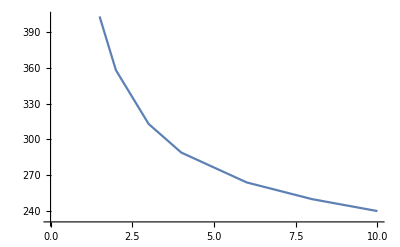

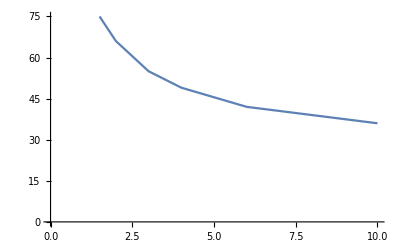

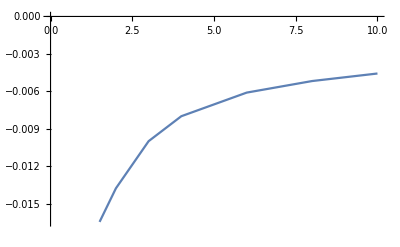

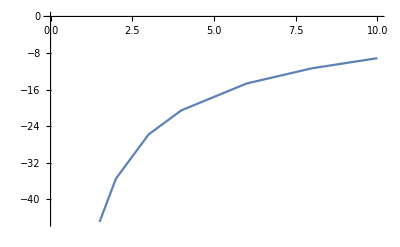

```mathematica
ListPlot[Transpose[{wflambdas,Flatten[Position[#,Min[#]]&/@pltp]}],Joined->True]
ListPlot[Transpose[{wflambdas,Flatten[Position[#,Min[#]]&/@plts]}],Joined->True]
ListPlot[Transpose[{wflambdas,Min[#]&/@pltp}],Joined->True]
ListPlot[Transpose[{wflambdas,Min[#]&/@plts}],Joined->True]
```

```mathematica
vEff[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=N[Rdis/Npoints];
energyMeV=(momentum^2)/TwoMyOverHBsq;

normsqu=NormTF[a00]^2;

Wmat=ConstantArray[0,{Npoints,Npoints}];

Do[
(*If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,*)

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;

amat=DiagonalMatrix[Table[VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];

wmat=Table[WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 
(*Print[(Chop[cij (amat+wmat)])[[1;;4,1;;4]]//MatrixForm];*)
Wmat=Wmat+cij (amat+wmat);

(*]*)
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

Dmat=DiagonalMatrix[Table[((Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Dmat+Wmat;
Amat
]
```

```mathematica
wfCores=RefCoreU;
pltListFull={};
Do[

nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==wflambdas[[nwf]]&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;
C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
mycore=wfCores[[nwf]];
rMax=5;nGrid=80;
pplot=Sqrt[mh2 ErangeMeV[[1]]];
ve=Chop[vEff[rMax,nGrid,pplot,1,λ,C0,D0,mycore,mh2]];
AppendTo[pltListFull,Diagonal[ve]];

,{nwf,Range[Length[wflambdas]]}]

rMin=N[rMax/nGrid];dr=N[rMax/nGrid];
Export["/tmp/nonLocal_V_nuclear_ref.dat",Transpose[Prepend[pltListFull,Range[rMin,rMax,dr]]],"Table"];
```

```mathematica
a0=5.156807805;r0=2.842442277;a1=-7.568032723;r1=3.75103428;
```

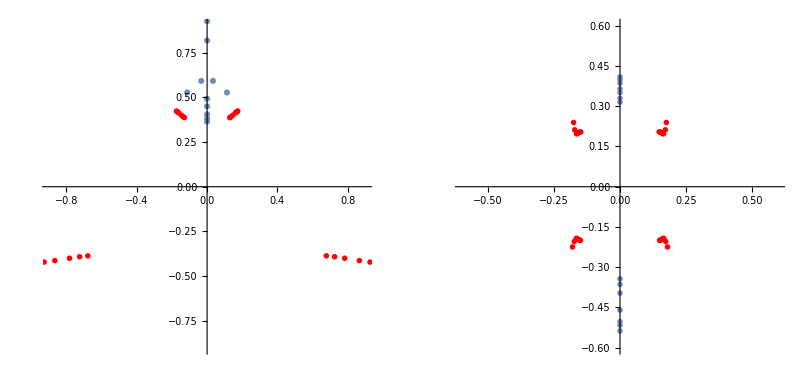

```mathematica
mrks=exportdata[[All,1]];
polesSar=Flatten[p/.NSolve[-1/(#[[1]])+(#[[2]])/2 p^2-I p==0,p]&/@exportdata[[All,4;;5]]];
polesSarp=Flatten[p/.NSolve[-1/(#[[1]])+(#[[2]])/2 p^2+#[[3]] p^4-I p==0,p]&/@exportdata[[All,8;;10]]];
polesPar=Flatten[p/.NSolve[-1/(#[[1]])+(#[[2]])/2 p^2-I p^3==0,p]&/@exportdata[[All,6;;7]]];
polesParp=Flatten[p/.NSolve[-1/(#[[1]])+(#[[2]])/2 p^2+#[[3]] p^4-I p^3==0,p]&/@exportdata[[All,11;;13]]];
GraphicsGrid[{{
Show[
ComplexListPlot[polesSarp,PlotMarkers->{Automatic,Scaled[0.04]},PlotStyle->{Red},PlotRange->{{-.9,.9},{-.9,.9}}],
ComplexListPlot[polesSar,PlotMarkers->Automatic,PlotStyle->Opacity[0.9]]
]
,
Show[
ComplexListPlot[polesParp,PlotMarkers->{Automatic,Scaled[0.04]},PlotStyle->{Red,Opacity[1]},PlotRange->{{-.6,.6},{-.6,.6}}],
ComplexListPlot[polesPar,PlotMarkers->{Blue,Scaled[0.015]},PlotStyle->Opacity[0.9]]
]
}}]
(*Solve[-1/a1+r1/2 p^2-I p^3==0,p,Complexes]
FindRoot[-1/a1+r1/2 p^2-I p^3,{p,3+I}]*)
```

```mathematica
exportdata[[All,4;;5]]//MatrixForm
exportdata[[All,8;;10]]//MatrixForm
```

(3.62755 | 1.89736
3.36771 | 1.68921
3.25547 | 1.52669
3.30389 | 1.45432
3.37753 | 1.32778
3.40322 | 1.19733
3.38762 | 1.03985)

(3.62755 | 1.89758 | -0.869898
3.36771 | 1.68949 | -1.14083
3.25547 | 1.52705 | -1.43034
3.30389 | 1.45473 | -1.67126
3.37753 | 1.3283 | -2.11405
3.40322 | 1.19795 | -2.51594
3.38762 | 1.04057 | -2.91733)

```mathematica
polesPar//MatrixForm
polesParp//MatrixForm
```

(0.+0.364512 ⅈ
0.-0.502745 ⅈ
0.-1.32571 ⅈ
0.+0.399795 ⅈ
0.-0.537489 ⅈ
0.-1.5606 ⅈ
0.+0.409561 ⅈ
0.-0.51609 ⅈ
0.-1.98416 ⅈ
0.+0.385944 ⅈ
0.-0.459744 ⅈ
0.-2.40429 ⅈ
0.+0.350671 ⅈ
0.-0.396656 ⅈ
0.-3.02481 ⅈ
0.+0.329464 ⅈ
0.-0.363961 ⅈ
0.-3.47599 ⅈ
0.+0.315298 ⅈ
0.-0.34319 ⅈ
0.-3.87945 ⅈ)

(-0.18001-0.224506 ⅈ
-0.175982+0.239565 ⅈ
0.175982+0.239565 ⅈ
0.18001-0.224506 ⅈ
-0.173359-0.204141 ⅈ
-0.17186+0.212111 ⅈ
0.17186+0.212111 ⅈ
0.173359-0.204141 ⅈ
-0.165885-0.192358 ⅈ
-0.165048+0.197452 ⅈ
0.165048+0.197452 ⅈ
0.165885-0.192358 ⅈ
-0.162495-0.193319 ⅈ
-0.161566+0.198206 ⅈ
0.161566+0.198206 ⅈ
0.162495-0.193319 ⅈ
-0.157578-0.196838 ⅈ
-0.156392+0.201762 ⅈ
0.156392+0.201762 ⅈ
0.157578-0.196838 ⅈ
-0.153636-0.199024 ⅈ
-0.152266+0.203936 ⅈ
0.152266+0.203936 ⅈ
0.153636-0.199024 ⅈ
-0.15012-0.19971 ⅈ
-0.148664+0.204461 ⅈ
0.148664+0.204461 ⅈ
0.15012-0.19971 ⅈ)